# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
Get["/home/miguel/Desktop/MINIPC/Prethermalization/QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Entanglement

```mathematica
(*2. Parameters*)
L=6;
J=1;
g=2.;
hlist=Sort[Append[Table[10^i,{i,-6,-1,0.5}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,-1,10,0.0050}]];
tlist//Length
hlist//Length
```

2201

12

```mathematica
states=Table[RandomChainProductState[L],{10}];
```

```mathematica
states=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{100}];
```

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[-1]];
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];]
```

{0.355555,Null}

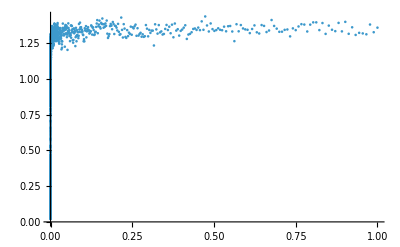

```mathematica
ListPlot[Transpose[{tlist,Mean[data]}],PlotRange->All]
```

## Exporting files

```mathematica
(* ===0) OUTPUT FOLDER+HELPERS (add this BEFORE the Do loop)===*)
outDir=FileNameJoin[{NotebookDirectory[],"SRN_entropies"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*file-safe tag for h values,e.g.0.001->"h_0p001"*)
hTag[h_?NumericQ]:="h_"<>StringReplace[ToString@NumberForm[h,{Infinity,10}],{"."->"p","-"->"m"," "->""}];
(*metadata to write once at the end*)
runMeta=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"tlist"->tlist,"NumStates"->Length[states],"TimestampStart"->DateString[{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}],"WolframVersion"->$Version|>;
(*optional:keep a small per-h timing log*)
perHLog=Association[];
(*safe numeric tag for g (unchanged if you already added it)*)
gTag[x_?NumericQ]:=Module[{d=IntegerString[Floor[FractionalPart[x]*10^4+0.5],10,4]},"1p"<>d];
(*filename base using the INDEX ih,zero-padded to 2 digits*)
baseNameIdx[ih_Integer?Positive]:=StringJoin["SRN_entropies_","L",ToString[L],"_","J",ToString[J],"_","g",gTag[g],"_","h_",IntegerString[ih,10,2]  (*i01,i02,...*)];
```

```mathematica
results={};
Do[
Print["Computing for h = "<>ToString[hlist[[ih]]]];
h=hlist[[ih]];
(*Your step 4:Hamiltonian and evolvers (UNCHANGED)*)Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[1]]];
{oddEigvals,oddEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[2]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*Local (non-parallel) worker using the evolvers for THIS h—UNCHANGED*)entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];
(* ===Only addition:time+export per h===*)
{dt,currentResults}=AbsoluteTiming[ParallelTable[entanglementWorker[state],{state,states}]];
AppendTo[results,currentResults];
perHLog[h]=<|"Seconds"->dt,"ResultShape"->Dimensions[currentResults]|>;
(*build trajectories:one {t,S(t)} table per state*)
trajectories=Map[Transpose[{tlist,#}]&,currentResults];
Export[FileNameJoin[{outDir,baseNameIdx[ih]<>".mx"}],trajectories,"MX"];

,{ih,Length[hlist]}];

(* ===Write metadata once at the end===*)
runMetaFinal=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"NumStates"->Length[states],"PerHFiles"->AssociationThread[hlist,Table[baseNameIdx[i]<>".mx",{i,Length[hlist]}]]|>;
metadata=runMetaFinal;
Put[metadata,FileNameJoin[{outDir,"metadata.m"}]];
Print["Saved per-h .mx files and metadata.m to: ",outDir];
```

Computing for h = 0.

Computing for h =      -6
1. 10

Computing for h =           -6
3.16228 10

Computing for h = 0.00001

Computing for h = 0.0000316228

Computing for h = 0.0001

Computing for h = 0.000316228

Computing for h = 0.001

Computing for h = 0.00316228

Computing for h = 0.01

Computing for h = 0.0316228

Computing for h = 0.1

Saved per-h .mx files and metadata.m to: C:\Users\Miguel\Github\Entropy\Prethermalization\Late time ensembles\SRN_entropies

```mathematica
data=results;
```

```mathematica
plotsa={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plotsa,ploten];
,{h,Length[hlist]}];
```

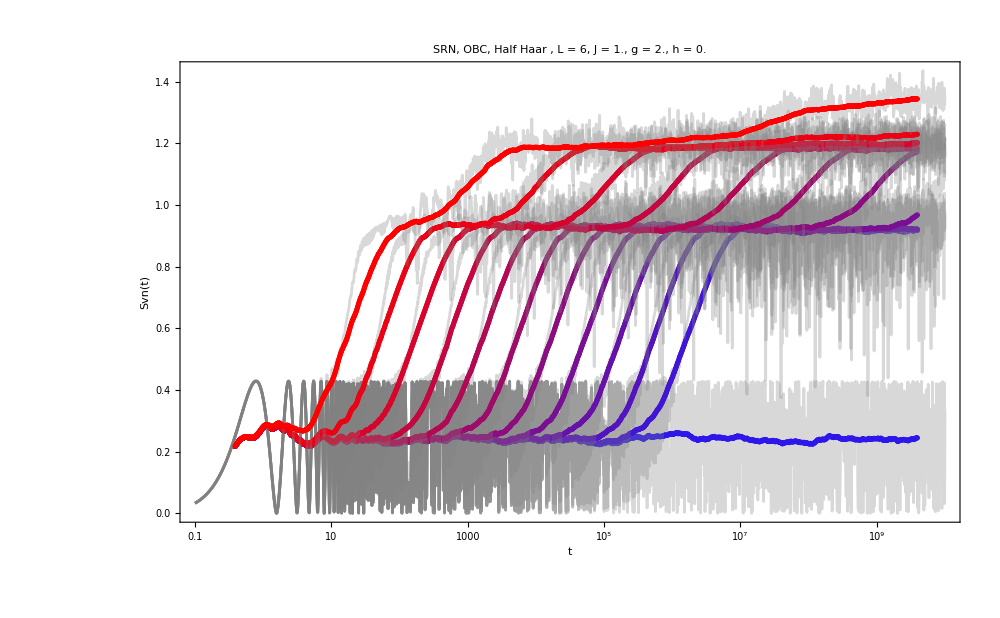

```mathematica
Show[plotsa,PlotRange->All]
```

# Individual bipartitions

```mathematica
(* =========1) Entanglement entropy for all bipartitions (unique up to complements)=========*)
ClearAll[getEntropyPartitioned];
getEntropyPartitioned[stateVec_,nSys_Integer?Positive]:=Module[{tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]],kmax=Floor[nSys/2],entByK,subs,sub,perm,tensorPerm,mat,sv,p,ppos},
entByK=Table[{},{kmax}];
Do[
subs=Subsets[Range[nSys],{k}];
entByK[[k]]=Table[perm=Join[sub,Complement[Range[nSys],sub]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
p=Clip[Chop[sv]^2,{0,Infinity}];
p=p/Total[p];
ppos=Select[p,#>0&];
-Total[ppos Log[ppos]],{sub,subs}];
,{k,1,kmax}];
entByK];
```

```mathematica
(* =========2) Parameters=========*)
L=8;
psi0=RandomChainProductState[L];
J=1;
```

```mathematica
g=0.5;
h=0.001;
tlist=N@Table[10.^i,{i,-1,10,0.005}];
(* =========3) Build symmetry-sector maps and full-state expander=========*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
(* =========4) Hamiltonian,parity blocks,and sector evolvers=========*)
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(* =========5) Worker:project->evolve in each sector->expand->entropies=========*)
ClearAll[entanglementWorker];
entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,nT},
{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
nT=Length[tlist];
ParallelMap[getEntropyPartitioned[ExpandFullStateFast[evenFinal[[#]],oddFinal[[#]]],L]&,Range[nT]]];
(* =========6) Distribute to kernels (after everything is defined)=========*)
DistributeDefinitions[L,tlist,evenMap,oddMap,ExpandFullStateFast,ProjectBlockVector,evenEvolver,oddEvolver,getEntropyPartitioned,entanglementWorker];
```

```mathematica
(* =========7) Run=========*)
AbsoluteTiming[data=entanglementWorker[psi0];]
```

{2.95401,Null}

```mathematica
ks=Range[Min[4,Floor[L/2]]];
limitsAll=LogLinearPlot[Evaluate@Table[pageEntropy[Min[k,L-k],Max[k,L-k]],{k,1,Floor[L/2]}],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
```

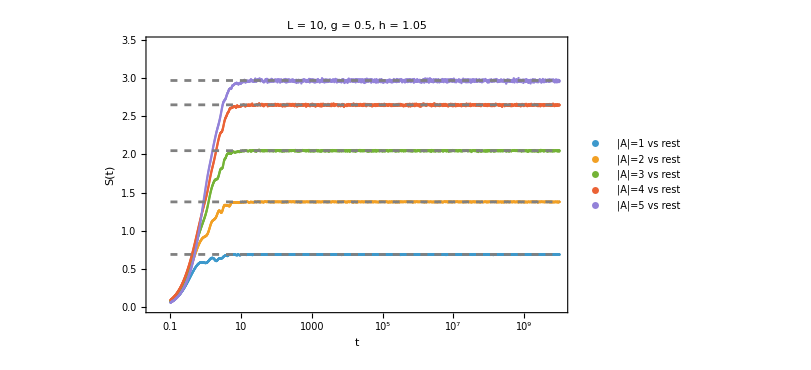

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

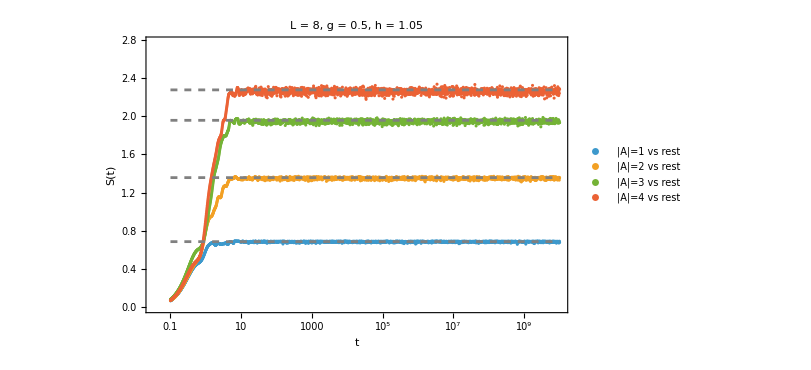

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

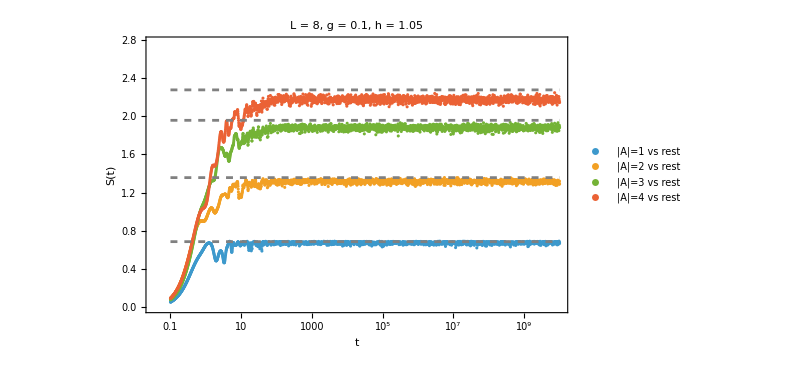

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

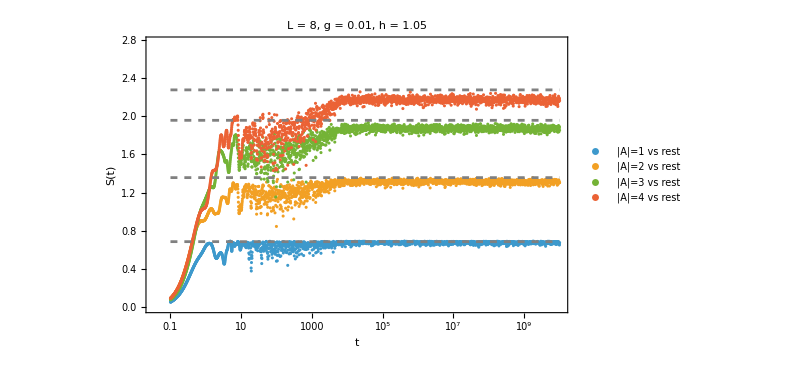

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

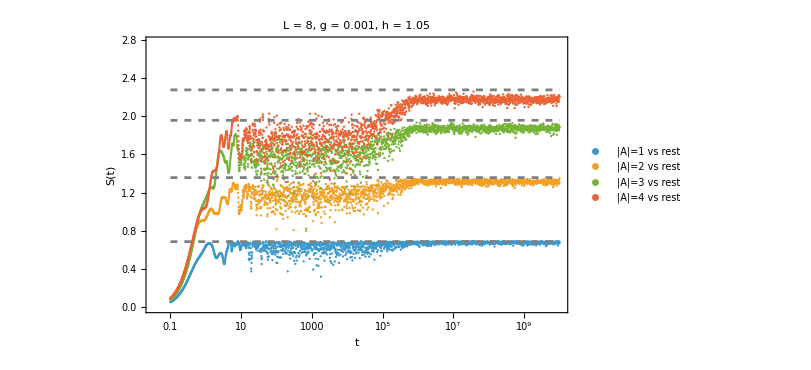

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

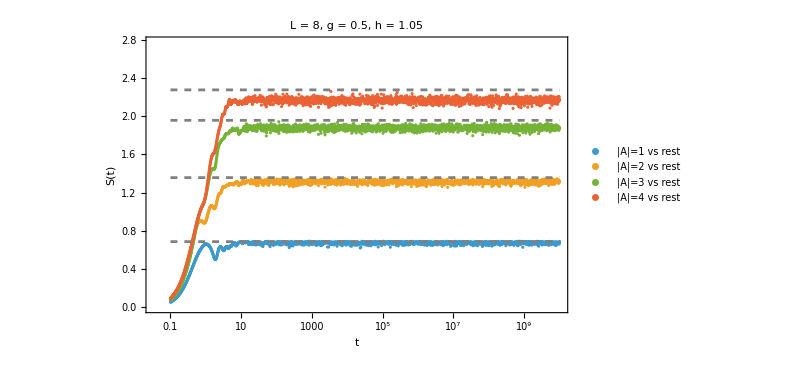

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

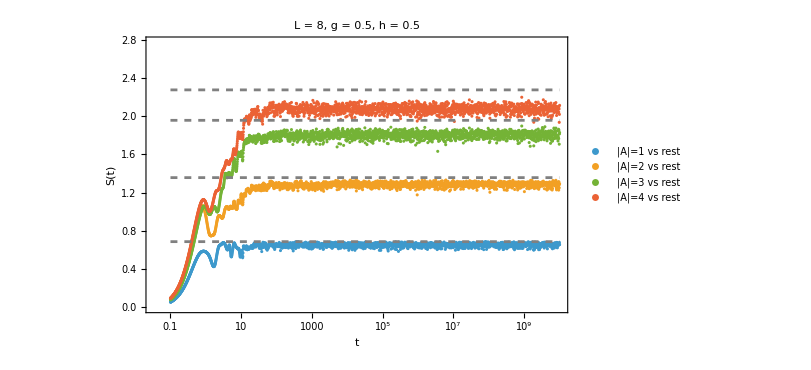

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

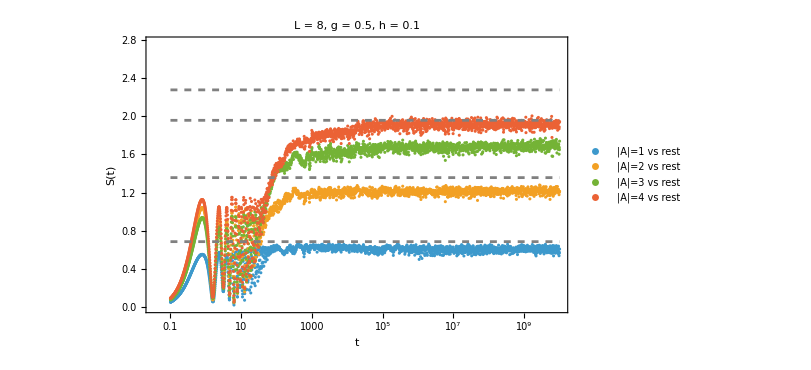

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

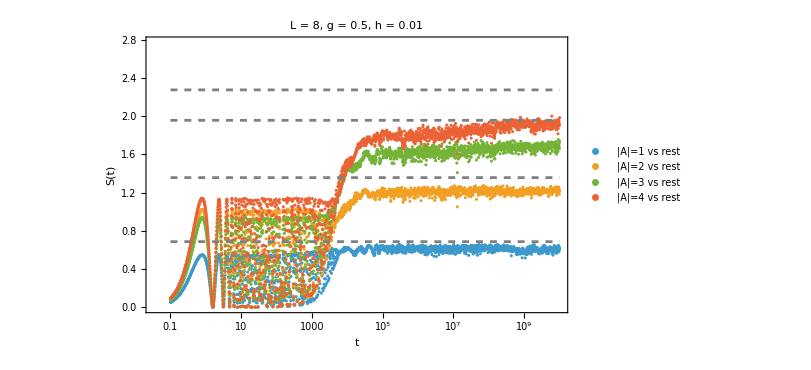

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

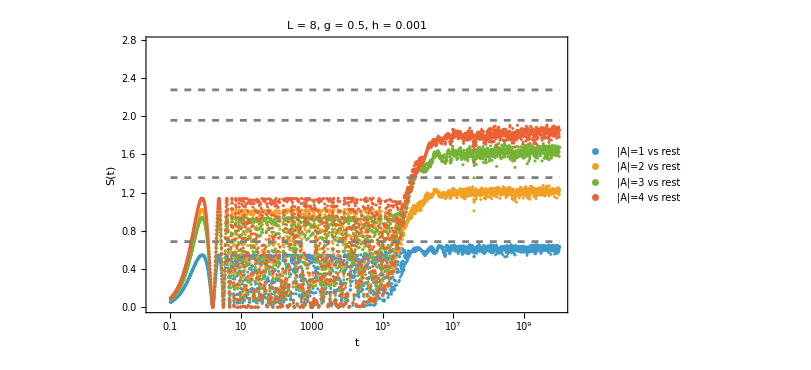

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

# Individual bipartitions

```mathematica
(* =========1) Entanglement entropy for all bipartitions (unique up to complements)=========*)
ClearAll[getEntropyPartitioned];
getEntropyPartitioned[stateVec_,nSys_Integer?Positive]:=Module[{tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]],kmax=Floor[nSys/2],entByK,subs,sub,perm,tensorPerm,mat,sv,p,ppos},
entByK=Table[{},{kmax}];
Do[
subs=Subsets[Range[nSys],{k}];
entByK[[k]]=Table[perm=Join[sub,Complement[Range[nSys],sub]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
p=Clip[Chop[sv]^2,{0,Infinity}];
p=p/Total[p];
ppos=Select[p,#>0&];
-Total[ppos Log[ppos]],{sub,subs}];
,{k,1,kmax}];
entByK];
```

```mathematica
(* =========2) Parameters=========*)
L=8;
psi0=RandomChainProductState[L];
J=1;
```

```mathematica
g=0.0001;
h=0.25;
tlist=N@Table[10.^i,{i,-1,10,0.001}];
(* =========3) Build symmetry-sector maps and full-state expander=========*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
(* =========4) Hamiltonian,parity blocks,and sector evolvers=========*)
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(* =========5) Worker:project->evolve in each sector->expand->entropies=========*)
ClearAll[entanglementWorker];
entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,nT},
{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
nT=Length[tlist];
ParallelMap[getEntropyPartitioned[ExpandFullStateFast[evenFinal[[#]],oddFinal[[#]]],L]&,Range[nT]]];
(* =========6) Distribute to kernels (after everything is defined)=========*)
DistributeDefinitions[L,tlist,evenMap,oddMap,ExpandFullStateFast,ProjectBlockVector,evenEvolver,oddEvolver,getEntropyPartitioned,entanglementWorker];
```

```mathematica
(* =========7) Run=========*)
AbsoluteTiming[data=entanglementWorker[psi0];]
```

{15.3833,Null}

```mathematica
ks=Range[Min[L/2,Floor[L/2]]];
limitsAll=LogLinearPlot[Evaluate@Table[pageEntropy[Min[k,L-k],Max[k,L-k]],{k,1,Floor[L/2]}],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
```

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[Transpose[{tlist,Sbar[[i]]}],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

-Graphics-

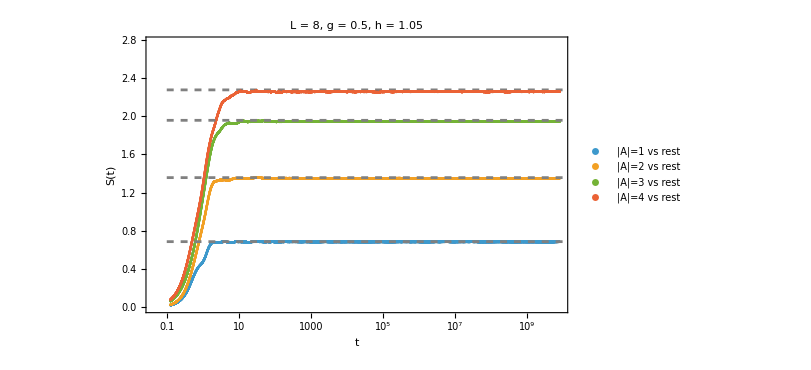

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

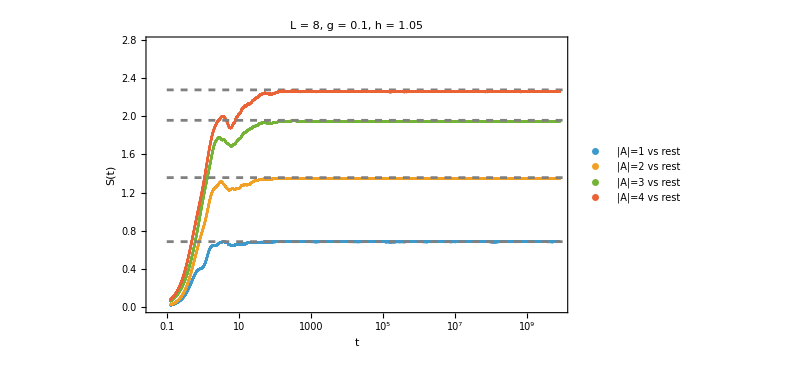

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

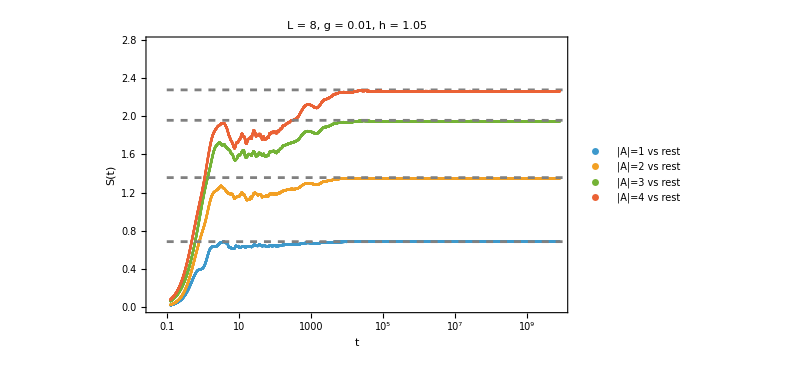

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

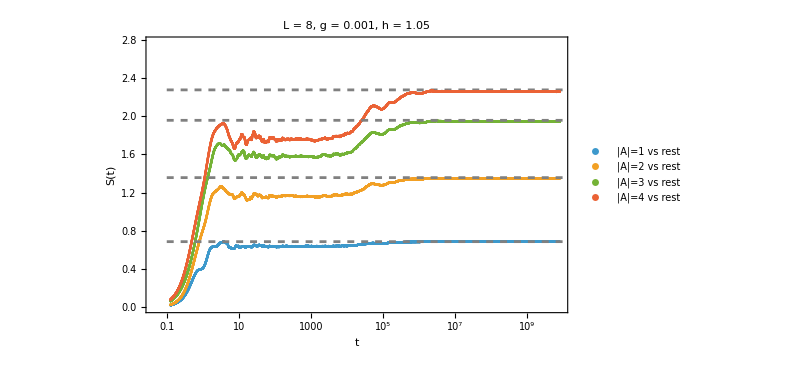

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

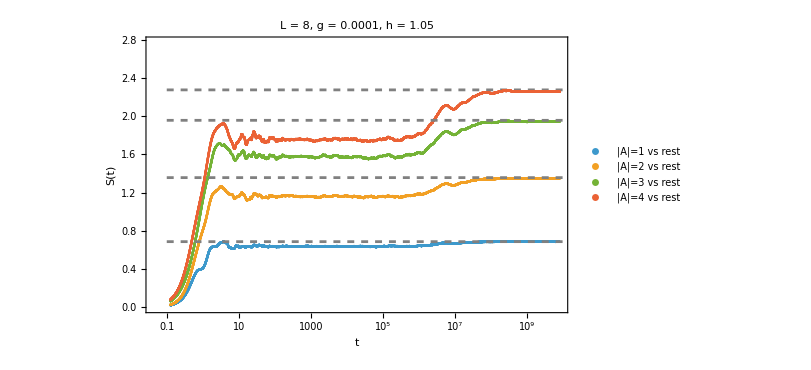

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

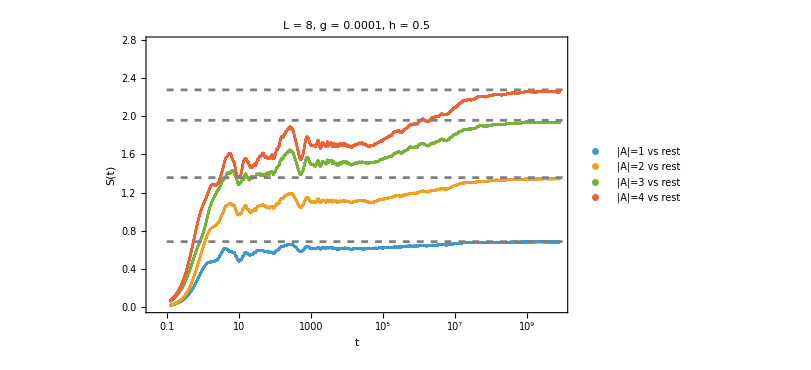

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

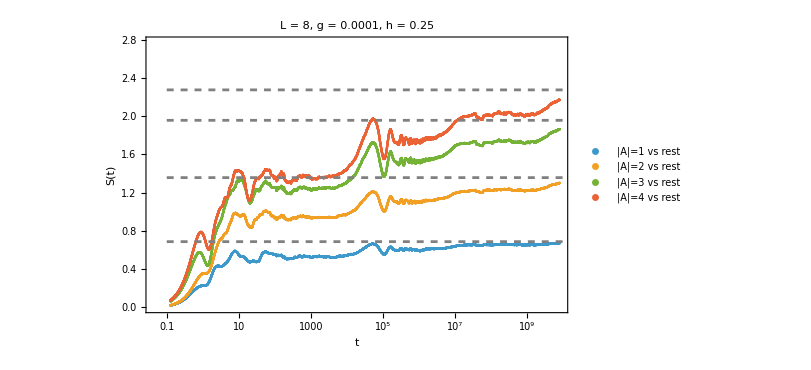

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```

# Individual bipartitions

```mathematica
(* =========1) Entanglement entropy for all bipartitions (unique up to complements)=========*)
ClearAll[getEntropyPartitioned];
getEntropyPartitioned[stateVec_,nSys_Integer?Positive]:=Module[{tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]],kmax=Floor[nSys/2],entByK,subs,sub,perm,tensorPerm,mat,sv,p,ppos},
entByK=Table[{},{kmax}];
Do[
subs=Subsets[Range[nSys],{k}];
entByK[[k]]=Table[perm=Join[sub,Complement[Range[nSys],sub]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
p=Clip[Chop[sv]^2,{0,Infinity}];
p=p/Total[p];
ppos=Select[p,#>0&];
-Total[ppos Log[ppos]],{sub,subs}];
,{k,1,kmax}];
entByK];
```

```mathematica
(* =========2) Parameters=========*)
L=8;
psi0=RandomChainProductState[L];
J=1;
```

```mathematica
g=0.5;
h=1.05;
tlist=N@Table[10.^i,{i,-1,10,0.001}];
(* =========3) Build symmetry-sector maps and full-state expander=========*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
(* =========4) Hamiltonian,parity blocks,and sector evolvers=========*)
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(* =========5) Worker:project->evolve in each sector->expand->entropies=========*)
ClearAll[entanglementWorker];
entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,nT},
{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
nT=Length[tlist];
ParallelMap[getEntropyPartitioned[ExpandFullStateFast[evenFinal[[#]],oddFinal[[#]]],L]&,Range[nT]]];
(* =========6) Distribute to kernels (after everything is defined)=========*)
DistributeDefinitions[L,tlist,evenMap,oddMap,ExpandFullStateFast,ProjectBlockVector,evenEvolver,oddEvolver,getEntropyPartitioned,entanglementWorker];
```

```mathematica
(* =========7) Run=========*)
AbsoluteTiming[data=entanglementWorker[psi0];]
```

{15.7715,Null}

```mathematica
ks=Range[Min[L/2,Floor[L/2]]];
limitsAll=LogLinearPlot[Evaluate@Table[pageEntropy[Min[k,L-k],Max[k,L-k]],{k,1,Floor[L/2]}],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
```

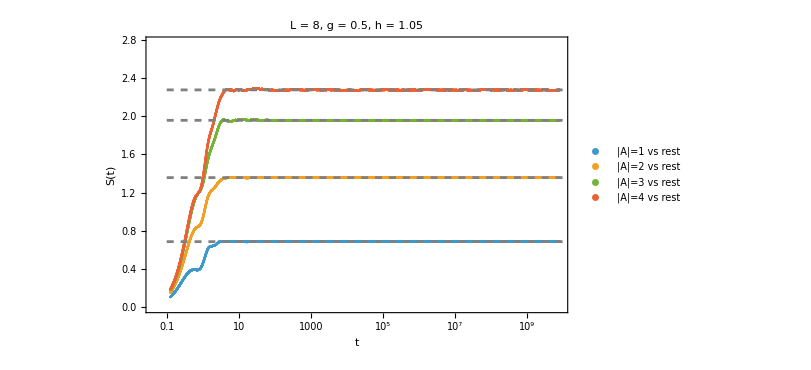

```mathematica
Sbar=Table[Mean/@data[[All,k]],{k,ks}];  (*one curve per k*)
curves=Table[MovingAverage[Transpose[{tlist,Sbar[[i]]}],200],{i,Length[ks]}];
Show[{ListLogLinearPlot[curves,Frame->True,FrameLabel->{"t","S(t)"},FrameStyle->Directive[Black,20],PlotLegends->(("|A|="<>ToString[#]<>" vs rest")&/@ks),PlotRange->{0,Max[ks] Log[2]},ImageSize->600,PlotLabel->Style["L = "<>ToString[L]<>", g = "<>ToString[g]<>", h = "<>ToString[h],25,Black]],limitsAll}]
```